```mathematica
Head[ListPlot]
```

Symbol

```mathematica
Times@@Range[100]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
f@@@Tuples[{a,b},2]
```

{f[a,a],f[a,b],f[b,a],f[b,b]}

```mathematica
ExpressionTree/@NestList[{#^#}&,x,4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Union[Cases[
Flatten[Table[{i^2/(j^2+1)},{i,20},{j,20}]],_Integer]]
```

{2,5,8,10,17,18,20,32,40,45,50,72,80,98,128,162,200}

```mathematica
Graph[Rule@@@Partition[Table[Mod[n^2+n,100],{n,100}],2,1]]
```

-Graphics-

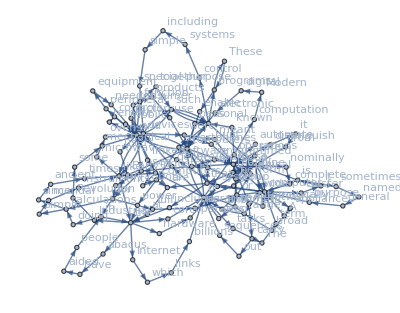

```mathematica
Graph[Rule@@@Partition[TextWords[WikipediaData["Computers"],200],2,1],VertexLabels->All]
```

```mathematica
FullForm[f@@#&/@{{1,2},{7,2},{5,4}}]
```

List[f[1,2],f[7,2],f[5,4]]

```mathematica
f@@@{{1,2},{7,2},{5,4}}
```

{f[1,2],f[7,2],f[5,4]}

# Chapter 34

```mathematica
Values[KeySort[Counts[IntegerDigits[3^100]]]]
```

{7,9,9,5,1,5,4,7,1}

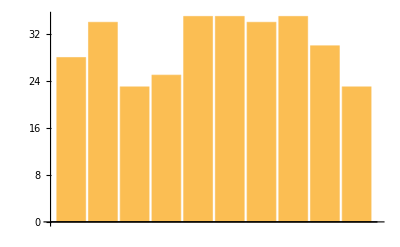

```mathematica
BarChart[Values[KeySort[Counts[IntegerDigits[2^1000]]]]]
```

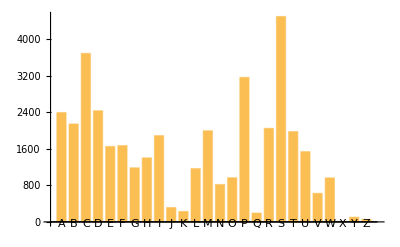

```mathematica
BarChart[KeySort[Counts[ToUpperCase[StringTake[WordList[],1]]]],ChartLabels->Automatic]
```

```mathematica
TakeLargest[KeySort[Counts[ToUpperCase[StringTake[WordList[],1]]]]
,5]
```

<|S→4502,C→3694,P→3168,D→2436,A→2397|>

```mathematica
#q/#u&@LetterCounts[WikipediaData["Computers"]]
```

63/1574

```mathematica
Keys[TakeLargest[Counts[TextWords[ExampleData[{"Text","AliceInWonderland"}]]]
,10]]
```

{the,and,a,to,she,of,was,Alice,in,it}